```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
dirName="/home/dan/ResearchLocal/"
SetDirectory[dirName];
```

/home/dan/ResearchLocal/

### Setup

```mathematica
eqTab={
ν==α cs h,
cs^2==(kb Tc)/(μ mp),
ρ==1/(√(2 π))Σ/h,
h==cs/Ω,
Tc^4==3/4 τ Tdisk^4,
τ==1/2 Σ κR,
ν Σ==mdot/(3π),
σ Tdisk^4==9/8 ν Σ Ω^2,
κR==κR0
};
rulesTab={ν>0,α>0,cs>0,h>0,kb>0,Tc>0,μ>0,mp>0,ρ>0,Σ>0,Ω>0,τ>0,Tdisk>0,τ>0,mdot>0,σ>0,κR>0,κR0>0,Tc>0};
```

### Known mdot, solving for Σ

```mathematica
sol1=Solve[Flatten[{eqTab,rulesTab}],{Tc,Tdisk,cs,ρ,h,κR,ν,τ,Σ},Reals];
sol3=Reduce[Flatten[{eqTab,rulesTab}],{Tc,Tdisk,cs,ρ,h,κR,ν,τ,Σ},Reals];
Table[ToRadicals[sol3[[i]]],{i,9,17}]//TableForm
```

Tc==((-1)^(2/5) (3/2)^(1/5) mdot^(2/5) mp^(1/5) κR0^(1/5) μ^(1/5) Ω^(3/5))/(2 kb^(1/5) π^(2/5) α^(1/5) σ^(1/5))
Tdisk==-(2^(3/4) kb^(1/4) π^(1/4) Tc^(5/4) α^(1/4))/(mdot^(1/4) mp^(1/4) κR0^(1/4) μ^(1/4) Ω^(1/4))
cs==(√((mdot Tdisk^4 κR0 Ω)/(Tc^4 α)))/(2 √(2 π))
ρ==(mdot Ω^2)/(3 √2 cs^3 π^(3/2) α)
h==cs/Ω
κR==(4 √(2/π) Tc^4)/(3 h Tdisk^4 ρ)
ν==cs h α
τ==(4 Tc^4)/(3 Tdisk^4)
Σ==h √(2 π) ρ

### Known Σ, solving for mdot

```mathematica
sol2=Solve[Flatten[{eqTab,rulesTab}],{Tc,Tdisk,cs,ρ,h,κR,ν,τ,mdot},Reals];
sol4=Reduce[Flatten[{eqTab,rulesTab}],{Tc,Tdisk,cs,ρ,h,κR,ν,τ,mdot},Reals];
Table[ToRadicals[sol4[[i]]],{i,9,17}]//TableForm
```

Tc==(3 (-1)^(2/3) kb^(1/3) α^(1/3) κR0^(1/3) Σ^(2/3) Ω^(1/3))/(4 mp^(1/3) μ^(1/3) σ^(1/3))
Tdisk==-(2^(3/4) Tc)/(3^(1/4) κR0^(1/4) Σ^(1/4))
cs==√((kb Tc)/(mp μ))
ρ==(9 cs α Σ^2 Ω^2)/(8 √(2 π) Tdisk^4 σ)
h==Σ/(√(2 π) ρ)
κR==(8 Tc^4)/(3 Tdisk^4 Σ)
ν==cs h α
τ==(4 Tc^4)/(3 Tdisk^4)
mdot==3 π ν Σ

### Plug in numbers and plot

```mathematica
kb=1;mp=1;μ=1;σ=1;
```

```mathematica
κR0=0.01;
G=1;M=(2π*100)^2;
α=0.01;
```

5

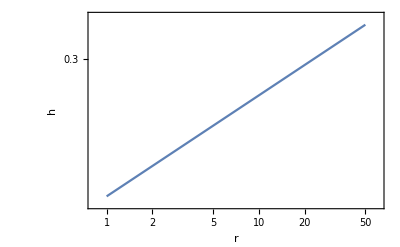

```mathematica
Table[LogLogPlot[(sol1[[1,5,2,1]]/r)/.{Ω->√((G M)/r^3),mdot->10^i}//N,{r,1,50},
Frame->True,
FrameLabel->{"r",sol1[[1,5,1]]}],
{i,0,10}]
```